```mathematica
s=Table[i+j,{i,3},{j,3}]
```

{{2,3,4},{3,4,5},{4,5,6}}

```mathematica
MatrixForm[s]
```

(2 | 3 | 4
3 | 4 | 5
4 | 5 | 6)

```mathematica
Array[a,4]
```

{a[1],a[2],a[3],a[4]}

```mathematica
Array[p,{3,2}]
```

{{p[1,1],p[1,2]},{p[2,1],p[2,2]},{p[3,1],p[3,2]}}

```mathematica
Dimensions[%]
```

{3,2}

```mathematica
DiagonalMatrix[{a,b,c}]
```

{{a,0,0},{0,b,0},{0,0,c}}

```mathematica
MatrixForm[%]
```

(a | 0 | 0
0 | b | 0
0 | 0 | c)

```mathematica
m
```

m

```mathematica
m={{a,b},{c,d}}
```

{{a,b},{c,d}}

```mathematica
MatrixForm[m]
```

(a | b
c | d)

```mathematica
Det[m]
```

-b c+a d

```mathematica
Transpose[m]
```

{{a,c},{b,d}}

```mathematica
Inverse[m]
```

{{d/(-b c+a d),-b/(-b c+a d)},{-c/(-b c+a d),a/(-b c+a d)}}

```mathematica
r= Table[i+j+1,{i,3},{j,3}]
```

{{3,4,5},{4,5,6},{5,6,7}}

```mathematica
p=MatrixForm[r]
```

(3 | 4 | 5
4 | 5 | 6
5 | 6 | 7)

```mathematica
Eigenvalues[p]
```

Eigenvalues[(3 | 4 | 5
4 | 5 | 6
5 | 6 | 7)]

```mathematica
Eigenvalues[%]
```

Eigenvalues[Eigenvalues[(3 | 4 | 5
4 | 5 | 6
5 | 6 | 7)]]

```mathematica
Eigenvalues[r]
```

{1/2 (15+√249),1/2 (15-√249),0}

```mathematica
IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
MatrixForm[%]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Eigenvalues[%]
```

{1,1,1}

```mathematica
Array[2^#&,5]
```

{2,4,8,16,32}

```mathematica
NestList[2*#&,1,15]
```

{1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768}

```mathematica
NestList[3 #&,2,6]
```

{2,6,18,54,162,486,1458}

```mathematica
NestList[Sqrt[1+#]&,1,5]
```

{1,√2,√(1+√2),√(1+√(1+√2)),√(1+√(1+√(1+√2))),√(1+√(1+√(1+√(1+√2))))}

```mathematica
N[%]
```

{1.,1.41421,1.55377,1.59805,1.61185,1.61612}

```mathematica
Append[%,2]
```

{1.,1.41421,1.55377,1.59805,1.61185,1.61612,2}

```mathematica
Reverse[%]
```

{2,1.61612,1.61185,1.59805,1.55377,1.41421,1.}

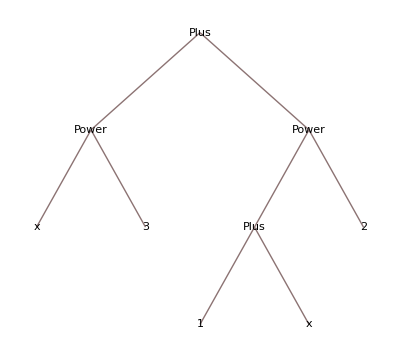

```mathematica
TreeForm[x^3+(1+x)^2]
```

```mathematica
Subscript[a, 6]=√(5 Subscript[a, 5]^4/64-3 Subscript[a, 4] Subscript[a, 5]^2/8+ Subscript[a, 4]^2/4+ Subscript[a, 3] Subscript[a, 5]/2  - Subscript[a, 2]);
Subscript[a, 7]= Subscript[a, 3] Subscript[a, 4]/4+ Subscript[a, 4] Subscript[a, 5]^3/16- Subscript[a, 4]^2 Subscript[a, 5]/8- Subscript[a, 3] Subscript[a, 5]^2/16-Subscript[a, 5]^5/128-Subscript[a, 1]/2;
Subscript[a, 5]= -8;
Subscript[a, 4]= 32;
Subscript[a, 3]= -78;
Subscript[a, 2]= 121;
Subscript[a, 1]= -110;
Subscript[a, 0]= 50;
Evaluate[Subscript[a, 7]]
```

-1

```mathematica
Subscript[a, 6]=√(5 Subscript[a, 5]^4/64-3 Subscript[a, 4] Subscript[a, 5]^2/8+ Subscript[a, 4]^2/4+ Subscript[a, 3] Subscript[a, 5]/2  - Subscript[a, 2]);

Subscript[a, 5]= 0;
Subscript[a, 4]= ω^2/(4 λ);
Subscript[a, 3]= 0;
Subscript[a, 2]= 0;
Subscript[a, 1]= -1/(8 λ);
Subscript[a, 0]= -(l (l+1))/(4 λ);
Evaluate[Subscript[a, 7]]
```

-1

```mathematica
Simplify[(x^2+(Subscript[b, 1]-p^(1/2))x+ Subscript[b, 0]-p^(1/2)Subscript[c, 0])(x^2+(Subscript[b, 1]+p^(1/2))x+Subscript[b, 0]+p^(1/2)Subscript[c, 0])]
```

(-√p x+x^2+b_0+x b_1-√p c_0) (x^2+b_0+x (√p+b_1)+√p c_0)

```mathematica
Simplify[%]
```

(-√p x+x^2+b_0+x b_1-√p c_0) (x^2+b_0+x (√p+b_1)+√p c_0)

```mathematica
FullSimplify[(-√p x+x^2+Subscript[b, 0]+x Subscript[b, 1]-√p Subscript[c, 0])* (x^2+Subscript[b, 0]+x (√p+Subscript[b, 1])+√p Subscript[c, 0])]
```

(b_0+x (-√p+x+b_1)-√p c_0) (b_0+x (√p+x+b_1)+√p c_0)

```mathematica
Times[(-√p x+x^2+Subscript[b, 0]+x Subscript[b, 1]-√p Subscript[c, 0]) ,(x^2+Subscript[b, 0]+x (√p+Subscript[b, 1])+√p Subscript[c, 0])]
```

(-√p x+x^2+b_0+x b_1-√p c_0) (x^2+b_0+x (√p+b_1)+√p c_0)

```mathematica
NSolve[{2 Subscript[b, 1]==-1, Subscript[b, 1]^2+2 Subscript[b, 0]-p== -19, 2(Subscript[b, 0] Subscript[b, 1]- p Subscript[c, 0])== -11, Subscript[b, 0]^2- p Subscript[c, 0]^2== 30},{Subscript[b, 1],Subscript[b, 0],p, Subscript[c, 0]}]
```

{{b_1→-0.5,b_0→5.5,p→30.25,c_0→0.0909091},{b_1→-0.5,b_0→-8.5,p→2.25,c_0→4.33333},{b_1→-0.5,b_0→-6.5,p→6.25,c_0→1.4}}